# Coordinate Transform and Jacobian

```mathematica
(* 2D example *)
u[x_,y_]:=x+y
v[x_,y_]:=x-y
(* the Jacobian *)
J= {{D[u[x,y],x], D[u[x,y],y]},{D[v[x,y],x],D[v[x,y],y]}};
J//MatrixForm
Det[J]//Simplify
```

(1 | 1
1 | -1)

-2

```mathematica
f[x_]:=π/2
```

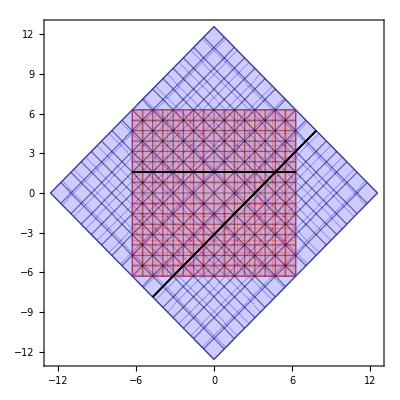

```mathematica
ParametricPlot[{{u[x,y],v[x,y]},{x,y},{x,f[x]},{u[x,f[x]],v[x,f[x]]}},{x,-2π,2π},{y,-2π,2π},AspectRatio->1,PlotRange->Full,PlotStyle->{Blue,Red}]
```

```mathematica
J.{D[t,t],D[2,t]}
```

{1,1}

```mathematica
(* Inverse *)
Jinv = Inverse[J];
Jinv//MatrixForm
Det[Jinv]
X[U_,V_]:=Jinv[[1,1]]U+Jinv[[1,2]]V
Y[U_,V_]:=Jinv[[2,1]]U+Jinv[[2,2]]V
```

(3/7 | 1/7
-1/7 | 2/7)

1/7

```mathematica
g[U_]:=U/2+7
```

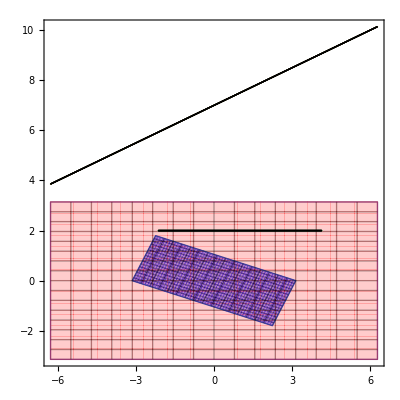

```mathematica
ParametricPlot[{{X[U,V],Y[U,V]},{U,V},{U,g[U]},{X[U,g[U]],Y[U,g[U]]}},{U,-2π,2π},{V,-π,π},AspectRatio->1,PlotRange->Full,PlotStyle->{Blue,Red}]
```